```mathematica
(* Look at stable distribution and infer what best payoff cap is based on underlying distr params *)
```

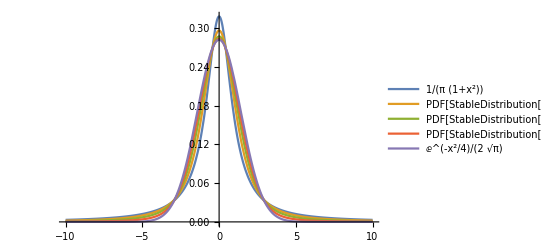

```mathematica
Plot[Table[PDF[StableDistribution[1,a,0,0,1],x],{a,{1.0,1.25, 1.5, 1.75, 2.0}}]//Evaluate,{x,-10,10}, PlotLegends->"Expressions"]
```

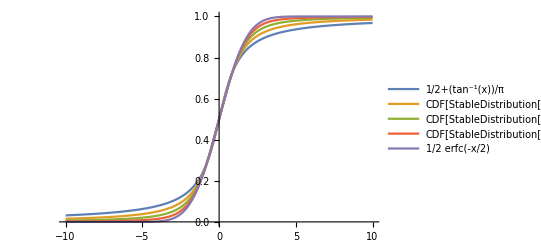

```mathematica
Plot[Table[CDF[StableDistribution[1,a,0,0,1],x],{a,{1.0,1.25, 1.5, 1.75, 2.0}}]//Evaluate,{x,-10,10}, PlotLegends->"Expressions"]
```

```mathematica
(* For alpha of 0.05, can essentially put cap on x as CDF(1-alpha). Which ultimately relates payoff cap to VaR metric *)
```

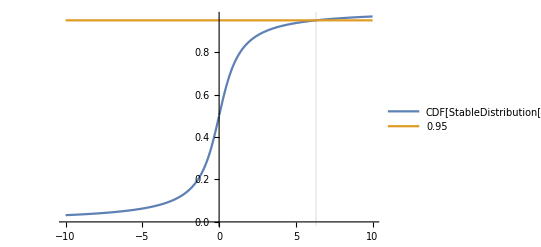

```mathematica
Plot[{CDF[StableDistribution[1,1.0,0,0,1],x], 0.95},{x,-10,10},GridLines->{{6.313751514675042},{}}, PlotLegends->"Expressions"]
```

```mathematica
Solve[CDF[StableDistribution[1,1.0,0,0,1], x] == 0.95, x]
```

{{x→6.31375}}

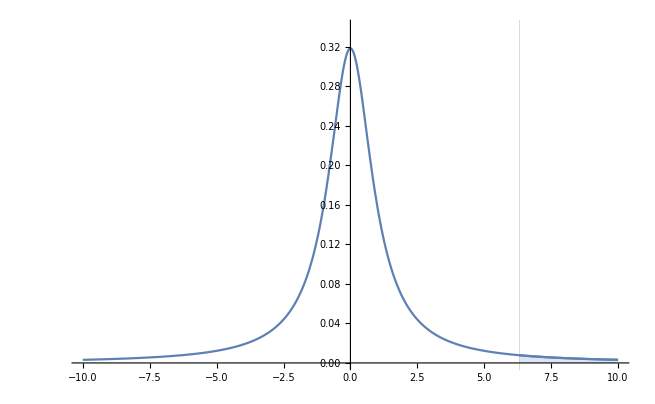

```mathematica
Show[Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,-10,10},GridLines->{{6.313751514675042},{}}, PlotLegends->"Expressions", PlotRange -> {0, 0.34}], Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,6.313751514675042,10}, PlotRange -> {0, 0.34}, Filling->Axis]]
```

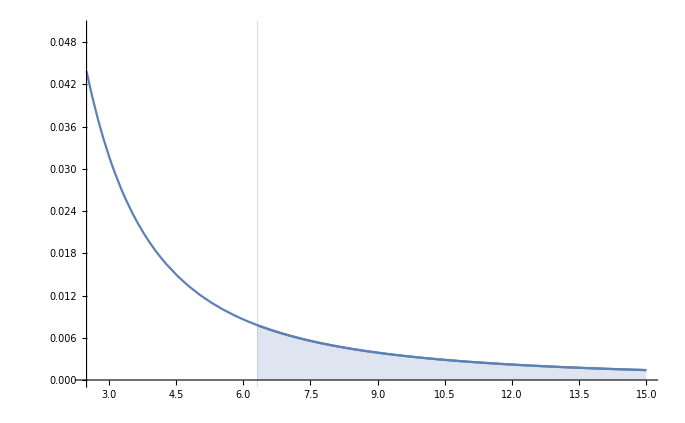

```mathematica
Show[Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,2.5,15},GridLines->{{6.313751514675042},{}}, PlotLegends->"Expressions", PlotRange -> {0,0.05}], Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,6.313751514675042,15}, PlotRange -> {0,0.05}, Filling -> Axis]]
```

```mathematica
(* Payoff to a shorter for a bearish OVL trade on inverse market: PnL = N * P(0) * [1/P(t) - 1/P(0)]; where P is # ETH / # OVL *)
```

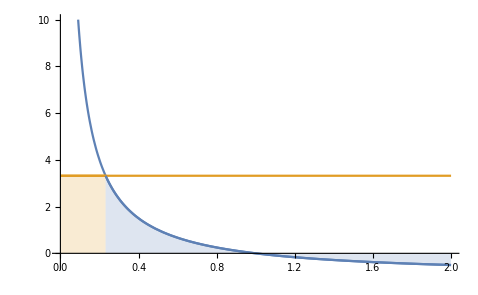

```mathematica
Show[Plot[{1/x - 1, Exp[1.2]},{x,0,2}, PlotRange -> {10,-2.5}], Plot[{, Exp[1.2]},{x,0,1/(Exp[1.2] + 1)}, Filling->Axis], Plot[{1/x - 1},{x,1/(Exp[1.2] + 1),2}, Filling->Axis]]
```

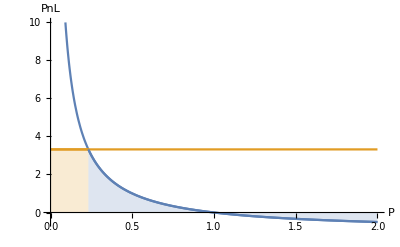

```mathematica
Show[%86,AxesLabel->{HoldForm[P],HoldForm[PnL]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Exp[1.2]
```

3.32012

```mathematica
1/(Exp[1.2] + 1)
```

0.231475

```mathematica
(* TODO: Get some actual numbers for e^X Levy process from fitting. smaller uncertainty level alpha used, means greater confidence in X max, and larger payoff cap to cut off tails with. This we might need considering vol factors from norm fitting were on order of 1e-7. Exp[1e-7 * 6.313751514675042 * 144 * 7] = 1.00063663 is a very small 7d payoff cap of about 100% on position. Likely want payoff cap of around 10x over span of 7 days, which gives Log[10] of 2.30259 max in exponent. Then know that 10x * OI imb cap is max amount we can print for one cycle, then we adjust cap down accordingly depending on prior printing on rolling 7d basis or something to strictly meet inflation goals *)
```

```mathematica
Exp[10^(-7) * 6.313751514675042 * 144*7]
```

1.00064

```mathematica
Log[10]
```

Log[10]

```mathematica
N[Log[10]]
```

2.30259

```mathematica
(* Inverse market payoff *)
```

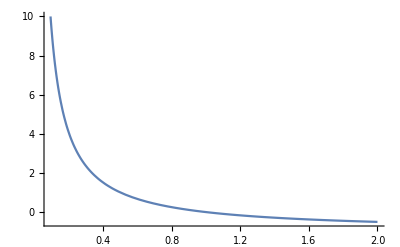

```mathematica
Plot[{1/x - 1},{x,0,2},GridLines->{{},{}}, PlotLegends->"Expressions", PlotRange -> {10,-2.5}]
```

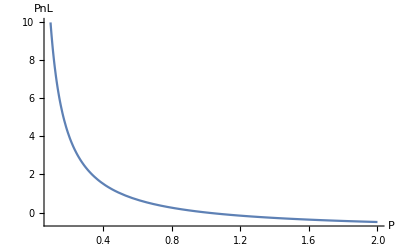

```mathematica
Show[%87,AxesLabel->{HoldForm[P],HoldForm[PnL]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

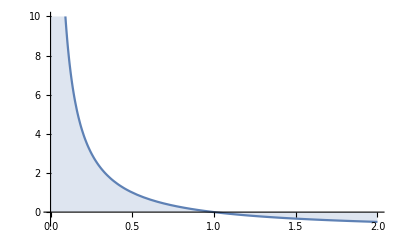

```mathematica
Plot[{1/x - 1},{x,0,2},GridLines->{{},{}}, PlotLegends->"Expressions", PlotRange -> {10,-2.5}, Filling->Axis]
```

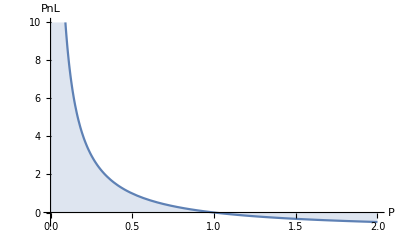

```mathematica
Show[%93,AxesLabel->{HoldForm[P],HoldForm[PnL]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```